# DA model

## version zero

This model corresponds to the IFF model in Schulze et al. eLife 2015;4:e06694. DOI: 10.7554/eLife.06694

```mathematica
Step[t_,t0_,τ_]=(Tanh[(t-t0)/τ]+1)/2;
Pulse[t_,t0_,tlen_,τ_]=Step[t,t0,τ](1-Step[t,t0+tlen,τ]);
Signal[t_,Sbackground_,Samplitude_,tStart_,tDuration_,tSharp_]=Sbackground +Samplitude Pulse[t,tStart,tDuration,tSharp];
```

```mathematica
eq={
z'[t]==x[t]-a z[t],
y'[t]== x[t]-b y[t],
τ/(1+β z[t]) r'[t]==α y[t]/(1+β z[t])-r[t]};
init={z[0]==z0,y[0]==y0,r[0]==r0};
par={a->0.1,b->10,τ->200,α->10000,β->100,z0->0,y0->0,r0->0,tStart->40,tDuration->5,tSharp->0.1,tMax->80};
eqs=Join[eq,init]/.par/.x[t]->Signal[t,Sbackground,Samplitude,tStart,tDuration,tSharp]/.par;
```

```mathematica
sol=ParametricNDSolveValue[eqs,{z,y,r},{t,0,(tMax/.par)},{Sbackground,Samplitude},Method->"Automatic",MaxSteps->10^6];
```

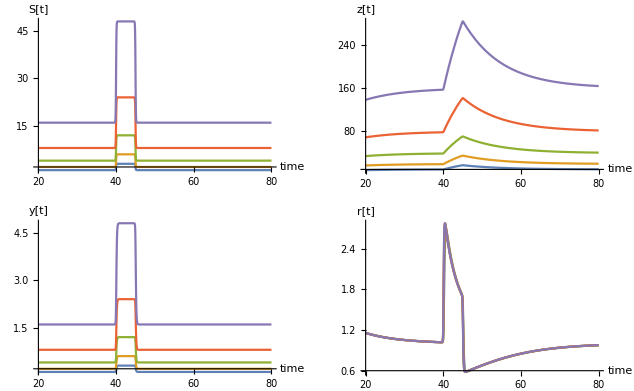

```mathematica
factors={1,2,4,8,16}1;
tMin=20;
GraphicsGrid[{{Plot[Evaluate[Table[Signal[t,S0,2S0,tStart,tDuration,tSharp]/.par,{S0,factors }]],{t,tMin,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","S[t]"}],
Plot[Evaluate[Table[sol[S0,2 S0][[1]][t],{S0,factors }]],{t,tMin,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","z[t]"}]},
{Plot[Evaluate[Table[sol[S0,2 S0][[2]][t],{S0,factors }]],{t,tMin,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","y[t]"}],
Plot[Evaluate[Table[sol[S0,2 S0][[3]][t],{S0,factors }]],{t,tMin,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","r[t]"}]}}]
```